```mathematica
Needs["GREATER2`"];
```

(*GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents*)

```mathematica
(*"GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents"*)
```

```mathematica
Clear[G,c]
```

```mathematica
(* define our coordinates *)
X = {r,θ,ϕ,t,τ};
```

```mathematica
(* define a line element Half space to Anti-deSitter metric *)
ds2 =Expand[FullSimplify[ExpandAll[((c^2* dt^2 -(dr^2+ dθ^2 r^2+ dϕ^2 r^2 Sin[θ]^2))+(c^2* dτ^2))]]]
```

-dr^2+c^2 dt^2+c^2 dτ^2-dθ^2 r^2-dϕ^2 r^2 Sin[θ]^2

```mathematica
(* calculate metric tensor*)
gdd = Metric[ds2, X]
```

{{-1,0,0,0,0},{0,-r^2,0,0,0},{0,0,-r^2 Sin[θ]^2,0,0},{0,0,0,c^2,0},{0,0,0,0,c^2}}

```mathematica
TableForm[gdd]
```

-1 | 0 | 0 | 0 | 0
0 | -r^2 | 0 | 0 | 0
0 | 0 | -r^2 Sin[θ]^2 | 0 | 0
0 | 0 | 0 | c^2 | 0
0 | 0 | 0 | 0 | c^2

```mathematica
Det[gdd]
```

-c^4 r^4 Sin[θ]^2

```mathematica
Clear[c]
```

```mathematica
Length[cl]
```

0

```mathematica
(*G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
α=1/137.035999206;*)
```

```mathematica
Tr[gdd]
```

-1+2 c^2-r^2-r^2 Sin[θ]^2

```mathematica
(*Tetrahedral model*)
```

```mathematica
(* inverse metric of metric tensor *)
guu =IMetric[gdd]
```

{{-1,0,0,0,0},{0,-1/r^2,0,0,0},{0,0,-Csc[θ]^2/r^2,0,0},{0,0,0,1/c^2,0},{0,0,0,0,1/c^2}}

```mathematica
TableForm[guu]
```

-1 | 0 | 0 | 0 | 0
0 | -1/r^2 | 0 | 0 | 0
0 | 0 | -Csc[θ]^2/r^2 | 0 | 0
0 | 0 | 0 | 1/c^2 | 0
0 | 0 | 0 | 0 | 1/c^2

```mathematica
(*Compute the Ricci scalar *)
R = SCurvature[gdd, X]
```

0

```mathematica
Rbar= SCurvature[guu, X]
```

(2 (5+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^2

```mathematica
(* Gaussian curvature:*)
K=Tr[ExtrinsicCurvature[gdd,3, 1, X]]
```

0

```mathematica
Kbar=Tr[ExtrinsicCurvature[guu,3, 1, X]]
```

0

```mathematica
(* calcxulate full Riemann Curvature tensor*)
Rhijk=Riemann[guu,X];
TableForm[FullSimplify[ExpandAll[Rhijk]]]
```

0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2/r^4 | 0 | 0 | 0
2/r^4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 Csc[θ]^2)/r^4 | 0 | 0
0 | 0 | 0 | 0 | 0
(2 Csc[θ]^2)/r^4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 2/r^2 | 0 | 0 | 0
-2/r^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Csc[θ]^2 (1-1/r^4-2 Csc[θ]^2) | 0 | 0
0 | Csc[θ]^2 (1/r^4+Cot[θ]^2+Csc[θ]^2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 2/r^2 | 0 | 0
0 | 0 | 0 | 0 | 0
-2/r^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/r^4+Cot[θ]^2+Csc[θ]^2 | 0 | 0
0 | 1-1/r^4-2 Csc[θ]^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0

```mathematica
?Contract
```

```mathematica
TensorContract[Rhijk,{{2,4}}]
```

{{-2/r^4-(2 Csc[θ]^2)/r^4,0,0,0,0},{0,-2/r^2-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4,0,0,0},{0,0,-1/r^4-2/r^2-Cot[θ]^2-Csc[θ]^2,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
Rij={{-2/r^4-(2 Csc[θ]^2)/r^4,0,0,0,0},{0,-2/r^2-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4,0,0,0},{0,0,-1/r^4-2/r^2-Cot[θ]^2-Csc[θ]^2,0,0},{0,0,0,-1,0},{0,0,0,0,-1}}
```

{{-2/r^4-(2 Csc[θ]^2)/r^4,0,0,0,0},{0,-2/r^2-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4,0,0,0},{0,0,-1/r^4-2/r^2-Cot[θ]^2-Csc[θ]^2,0,0},{0,0,0,-1,0},{0,0,0,0,-1}}

```mathematica
R=TensorContract[Rij,{{1,2}}]
```

-2-3/r^4-4/r^2-Cot[θ]^2-Csc[θ]^2-(2 Csc[θ]^2)/r^4-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4

```mathematica
G0=Rij-(R/2)*guu+λ *guu
```

{{-2/r^4-λ-(2 Csc[θ]^2)/r^4,0,0,0,0},{0,-2/r^2-λ/r^2-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4,0,0,0},{0,0,-1/r^4-2/r^2-Cot[θ]^2-Csc[θ]^2-(λ Csc[θ]^2)/r^2,0,0},{0,0,0,-1+λ/c^2,0},{0,0,0,0,-1+λ/c^2}}

```mathematica
FullSimplify[ExpandAll[c^4 r^12*Det[G0]]]
```

-(c^2-λ)^2 (2+r^4 λ+2 Csc[θ]^2) (1+2 r^2+r^4 Cot[θ]^2+r^2 (r^2+λ) Csc[θ]^2) (r^2 (2+λ)-(-1+r^4) Csc[θ]^2+2 r^4 Csc[θ]^4)

```mathematica
(2 r^4 λ)/c^2-(1+r^2) (3+r^2 (1+λ))-Csc[θ]^2 (3+r^4+r^2 λ+2 r^4 Csc[θ]^2)/.r->N[Exp[I*Pi/4]]//Chop
```

(-1.-1. ⅈ) (3+(0.+1. ⅈ) (1+λ))-Csc[θ]^2 (2.+(0.+1. ⅈ) λ-2. Csc[θ]^2)

```mathematica
u=Union[Flatten[Table[λ/.Solve[(-1.000000000000000-1. ⅈ) (3+(0.+1. ⅈ) (1+λ))-Csc[θ]^2 (2.+(0.+1. ⅈ) λ-2. Csc[θ]^2)-2.0==0,λ],{θ,-N[Pi]+0.01,N[Pi],N[Pi/16]}]]]
```

{-1.9998-19996.7 ⅈ,-1.9998-19996.7 ⅈ,-1.9315-54.2007 ⅈ,-1.9315-54.2007 ⅈ,-1.91631-43.5654 ⅈ,-1.91631-43.5654 ⅈ,-1.72934-10.1308 ⅈ,-1.72934-10.1308 ⅈ,-1.70352-8.79505 ⅈ,-1.70352-8.79505 ⅈ,-1.46149-2.34193 ⅈ,-1.46149-2.34193 ⅈ,-1.43407-1.94465 ⅈ,-1.43407-1.94465 ⅈ,-1.21128+0.316715 ⅈ,-1.21128+0.316715 ⅈ,-1.18888+0.479969 ⅈ,-1.18888+0.479969 ⅈ,-1.02112+1.48179 ⅈ,-1.02112+1.48179 ⅈ,-1.00546+1.55927 ⅈ,-1.00546+1.55927 ⅈ,-0.895089+2.0474 ⅈ,-0.885512+2.08549 ⅈ,-0.885512+2.08549 ⅈ,-0.824144+2.3156 ⅈ,-0.819645+2.33157 ⅈ,-0.800056+2.39981 ⅈ}

```mathematica
Fit[u,{1,x},x]
```

(-2.09999-5581.66 ⅈ)+(0.0504534+285.892 ⅈ) x

```mathematica
Solve[(-2.099986407425567-5581.663969827871 ⅈ)+(0.05045344957443915+285.8922215946723 ⅈ) x==0,x]
```

{{x→19.5237-0.0038999 ⅈ}}

```mathematica
Abs[u]
```

{2.×10^8,2.×10^8,9.59901,9.59901,9.58583,9.58583,1.26476,1.26506,1.26506,2.25022,2.25053,2.25053,2.52982}

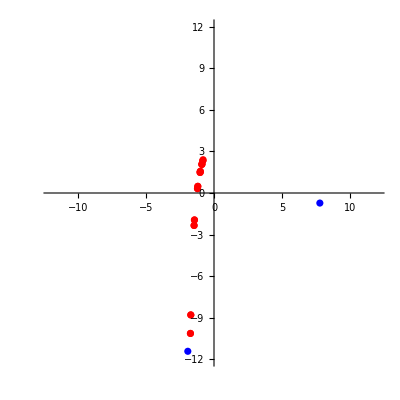

```mathematica
ComplexListPlot[{u,{(-1.9226021032088658-11.418454060340219 ⅈ),7.7708030233201155-0.7255034635181047 ⅈ}},PlotRange->{{-3,3},{-3,3}}*12/3,PlotStyle->{Red,Blue}]
```

```mathematica
Solve[2.225300112107237*^-21 λ-2.0000000000000004 (8.+1. λ)-2. (3+1. (1+λ))-2==0,λ]
```

{{λ→-6.5}}

```mathematica
v=Union[Flatten[Table[r/.Solve[(2 r^4 λ)/c^2-(1+r^2) (3+r^2 (1+λ))-Csc[θ]^2 (3+r^4+r^2 λ+2 r^4 Csc[θ]^2)-2==0,r]/.λ->u[[i]]/.θ->N[Pi/4],{i,Length[u]}]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{-0.795825-0.91717 ⅈ,-0.795825-0.91717 ⅈ,-0.788367-0.883284 ⅈ,-0.74645+0.858659 ⅈ,-0.74645+0.858659 ⅈ,-0.746252+0.852197 ⅈ,-0.745251+0.899372 ⅈ,-0.744975+0.902536 ⅈ,-0.744975+0.902536 ⅈ,-0.742717+0.921576 ⅈ,-0.742522+0.922891 ⅈ,-0.741633+0.928499 ⅈ,-0.734952+0.770272 ⅈ,-0.734952+0.770272 ⅈ,-0.731711+0.757424 ⅈ,-0.710797-0.712353 ⅈ,-0.710797-0.712353 ⅈ,-0.70353-0.702151 ⅈ,-0.70353-0.702151 ⅈ,-0.697704-1.3735 ⅈ,-0.697704-1.3735 ⅈ,-0.66101+0.605794 ⅈ,-0.66101+0.605794 ⅈ,-0.657023-1.42997 ⅈ,-0.657023-1.42997 ⅈ,-0.65672-0.646911 ⅈ,-0.652997-0.643162 ⅈ,-0.652997-0.643162 ⅈ,-0.646082+0.5849 ⅈ,-0.646082+0.5849 ⅈ,-0.629373-0.621225 ⅈ,-0.62752-0.619634 ⅈ,-0.62752-0.619634 ⅈ,-0.616294-0.610386 ⅈ,-0.615513-0.609767 ⅈ,-0.612173-0.607158 ⅈ,-0.451669+0.397701 ⅈ,-0.451669+0.397701 ⅈ,-0.425598+0.377249 ⅈ,-0.425598+0.377249 ⅈ,-0.211258-1.70734 ⅈ,-0.211258-1.70734 ⅈ,-0.20846+0.200152 ⅈ,-0.20846+0.200152 ⅈ,-0.186471+0.180385 ⅈ,-0.186471+0.180385 ⅈ,-0.171261-1.71595 ⅈ,-0.171261-1.71595 ⅈ,-0.00957552+0.00957462 ⅈ,-0.00957552+0.00957462 ⅈ,-0.000471581-1.73205 ⅈ,-0.000471581-1.73205 ⅈ,0.000471581+1.73205 ⅈ,0.000471581+1.73205 ⅈ,0.00957552-0.00957462 ⅈ,0.00957552-0.00957462 ⅈ,0.171261+1.71595 ⅈ,0.171261+1.71595 ⅈ,0.186471-0.180385 ⅈ,0.186471-0.180385 ⅈ,0.20846-0.200152 ⅈ,0.20846-0.200152 ⅈ,0.211258+1.70734 ⅈ,0.211258+1.70734 ⅈ,0.425598-0.377249 ⅈ,0.425598-0.377249 ⅈ,0.451669-0.397701 ⅈ,0.451669-0.397701 ⅈ,0.612173+0.607158 ⅈ,0.615513+0.609767 ⅈ,0.616294+0.610386 ⅈ,0.62752+0.619634 ⅈ,0.62752+0.619634 ⅈ,0.629373+0.621225 ⅈ,0.646082-0.5849 ⅈ,0.646082-0.5849 ⅈ,0.652997+0.643162 ⅈ,0.652997+0.643162 ⅈ,0.65672+0.646911 ⅈ,0.657023+1.42997 ⅈ,0.657023+1.42997 ⅈ,0.66101-0.605794 ⅈ,0.66101-0.605794 ⅈ,0.697704+1.3735 ⅈ,0.697704+1.3735 ⅈ,0.70353+0.702151 ⅈ,0.70353+0.702151 ⅈ,0.710797+0.712353 ⅈ,0.710797+0.712353 ⅈ,0.731711-0.757424 ⅈ,0.734952-0.770272 ⅈ,0.734952-0.770272 ⅈ,0.741633-0.928499 ⅈ,0.742522-0.922891 ⅈ,0.742717-0.921576 ⅈ,0.744975-0.902536 ⅈ,0.744975-0.902536 ⅈ,0.745251-0.899372 ⅈ,0.746252-0.852197 ⅈ,0.74645-0.858659 ⅈ,0.74645-0.858659 ⅈ,0.788367+0.883284 ⅈ,0.795825+0.91717 ⅈ,0.795825+0.91717 ⅈ}

```mathematica
Abs[v]
```

{1.21431,1.21431,1.18394,1.13775,1.13775,1.13275,1.16802,1.17028,1.17028,1.18361,1.18451,1.18833,1.06465,1.06465,1.05313,1.00632,1.00632,0.993967,0.993967,1.54055,1.54055,0.896616,0.896616,1.57369,1.57369,0.921832,0.916549,0.916549,0.871511,0.871511,0.884325,0.881888,0.881888,0.867403,0.866413,0.862204,0.601806,0.601806,0.568728,0.568728,1.72036,1.72036,0.288992,0.288992,0.259442,0.259442,1.72447,1.72447,0.0135412,0.0135412,1.73205,1.73205,1.73205,1.73205,0.0135412,0.0135412,1.72447,1.72447,0.259442,0.259442,0.288992,0.288992,1.72036,1.72036,0.568728,0.568728,0.601806,0.601806,0.862204,0.866413,0.867403,0.881888,0.881888,0.884325,0.871511,0.871511,0.916549,0.916549,0.921832,1.57369,1.57369,0.896616,0.896616,1.54055,1.54055,0.993967,0.993967,1.00632,1.00632,1.05313,1.06465,1.06465,1.18833,1.18451,1.18361,1.17028,1.17028,1.16802,1.13275,1.13775,1.13775,1.18394,1.21431,1.21431}

```mathematica
(*Lemniscate on complex axis*)
```

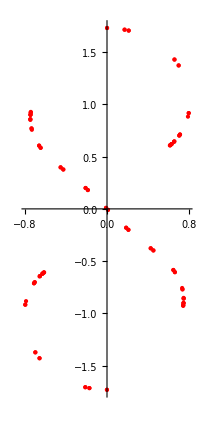

```mathematica
ComplexListPlot[v,PlotStyle->{Red,PointSize->Medium}]
```

```mathematica
c=2.99792458*10^(10)
```

2.99792×10^10

```mathematica
N[Cot[π/4]^2.]
```

1.

```mathematica
w=ExpandAll[r/.NSolve[-1-(c^2-λ)^2 (2+r^4 λ+2 Csc[θ]^2) (1+2 r^2+r^4 Cot[θ]^2+r^2 (r^2+λ) Csc[θ]^2) (r^2 (2+λ)-(-1+r^4) Csc[θ]^2+2 r^4 Csc[θ]^4)==0,r]/.λ->0/.θ->N[Pi/4]/.Csc[π/4]^2->2.0/.Cot[π/4]^2->1.0]
```

Root::deg: 1.+1.61552×10^42 Csc[θ]^2+1.61552×10^42 Csc[θ]^4+(3.23104×10^42+«1»+«1») «2»+(6.46209×10^42+4.84657×10^42 Csc[θ]^2+«3»+4.84657×10^42 Csc[θ]^6) #1^2+(0.+3.23104×10^42 Cot[θ]^2+3.23104×10^42 Cot[θ]^2 Csc[θ]^2+6.46209×10^42 Csc[θ]^4+6.46209×10^42 Csc[θ]^6) #1^3+(0.-1.61552×10^42 Cot[θ]^2 Csc[θ]^2-1.61552×10^42 Csc[θ]^4+1.61552×10^42 Cot[θ]^2 Csc[θ]^4+1.61552×10^42 Csc[θ]^6+3.23104×10^42 Cot[θ]^2 Csc[θ]^6+3.23104×10^42 Csc[θ]^8) #1^4 has fewer than 5 root(s) as a polynomial in #1.

Root::deg: 1.+1.61552×10^42 Csc[θ]^2+1.61552×10^42 Csc[θ]^4+(3.23104×10^42+«1»+«1») «2»+(6.46209×10^42+4.84657×10^42 Csc[θ]^2+«3»+4.84657×10^42 Csc[θ]^6) #1^2+(0.+3.23104×10^42 Cot[θ]^2+3.23104×10^42 Cot[θ]^2 Csc[θ]^2+6.46209×10^42 Csc[θ]^4+6.46209×10^42 Csc[θ]^6) #1^3+(0.-1.61552×10^42 Cot[θ]^2 Csc[θ]^2-1.61552×10^42 Csc[θ]^4+1.61552×10^42 Cot[θ]^2 Csc[θ]^4+1.61552×10^42 Csc[θ]^6+3.23104×10^42 Cot[θ]^2 Csc[θ]^6+3.23104×10^42 Csc[θ]^8) #1^4 has fewer than 6 root(s) as a polynomial in #1.

General::stop: Further output of Root::deg will be suppressed during this calculation.

Root::npoly: 9.69313×10^42+2.90794×10^43 #1+7.7545×10^43 #1^2.+8.72382×10^43 #1^3+8.72382×10^43 #1^4 is not a polynomial in #1.

General::stop: Further output of Root::npoly will be suppressed during this calculation.

Function::slot: Slot[1.] (in 1.+«10»+(1.61552×10^42 0+8.07761×10^41 0^2.-1.79751×10^21 0^3+0^4+3.23104×10^42 Cot[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2.+2. 0^3 Cot[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^2.-7.19004×10^21 0^2. Csc[0.785398]^2.+«17») Slot[1.]^3+«3»&) should contain a non-negative integer or string.

General::stop: Further output of Function::slot will be suppressed during this calculation.

{-0.349297+0.67479 ⅈ,0.349297-0.67479 ⅈ,-0.349297-0.67479 ⅈ,0.349297+0.67479 ⅈ,-0.453147+0.609925 ⅈ,0.453147-0.609925 ⅈ,-0.453147-0.609925 ⅈ,0.453147+0.609925 ⅈ,-1. √Root[1.+1.61552×10^42 Csc[0.785398]^2.-3.59502×10^21 0 Csc[0.785398]^2.+2. 0^2. Csc[0.785398]^2.+1.61552×10^42 Csc[0.785398]^4-3.59502×10^21 0 Csc[0.785398]^4+2. 0^2. Csc[0.785398]^4+(3.23104×10^42+1.61552×10^42 0-3.59502×10^21 0^2.+2. 0^3+6.46209×10^42 Csc[0.785398]^2.+1.61552×10^42 0 Csc[0.785398]^2.-3.59502×10^21 0^2. Csc[0.785398]^2.+2. 0^3 Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^4-3.59502×10^21 0^2. Csc[0.785398]^4+2. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]+(6.46209×10^42+3.23104×10^42 0-7.19004×10^21 0^2.+4. 0^3+4.84657×10^42 Csc[0.785398]^2.+7.26985×10^42 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.-3.59502×10^21 0^3 Csc[0.785398]^2.+2. 0^4 Csc[0.785398]^2.+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+3.23104×10^42 0 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^4-3.59502×10^21 0^3 Csc[0.785398]^4+2. 0^4 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+4.84657×10^42 Csc[0.785398]^6-1.07851×10^22 0 Csc[0.785398]^6+6. 0^2. Csc[0.785398]^6) Slot[1.]^2.+(1.61552×10^42 0+8.07761×10^41 0^2.-1.79751×10^21 0^3+0^4+3.23104×10^42 Cot[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2.+2. 0^3 Cot[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^2.-7.19004×10^21 0^2. Csc[0.785398]^2.+4. 0^3 Csc[0.785398]^2.+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.+6.46209×10^42 Csc[0.785398]^4-1.43801×10^22 0 Csc[0.785398]^4+8.07761×10^41 0^2. Csc[0.785398]^4-1.79751×10^21 0^3 Csc[0.785398]^4+0^4 Csc[0.785398]^4+6.46209×10^42 Csc[0.785398]^6+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6+3.23104×10^42 0 Csc[0.785398]^8-7.19004×10^21 0^2. Csc[0.785398]^8+4. 0^3 Csc[0.785398]^8) Slot[1.]^3+(3.23104×10^42 0+1.61552×10^42 0^2.-3.59502×10^21 0^3+2. 0^4-8.07761×10^41 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.+8.07761×10^41 0^3 Csc[0.785398]^2.-1.79751×10^21 0^4 Csc[0.785398]^2.+0^5 Csc[0.785398]^2.-1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.-1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+0^3 Cot[0.785398]^2. Csc[0.785398]^2.-1.61552×10^42 Csc[0.785398]^4+2.42328×10^42 0 Csc[0.785398]^4-5.39253×10^21 0^2. Csc[0.785398]^4+3. 0^3 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 Csc[0.785398]^6-3.59502×10^21 0 Csc[0.785398]^6+2. 0^2. Csc[0.785398]^6+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^6-7.19004×10^21 0 Cot[0.785398]^2. Csc[0.785398]^6+4. 0^2. Cot[0.785398]^2. Csc[0.785398]^6+3.23104×10^42 Csc[0.785398]^8-7.19004×10^21 0 Csc[0.785398]^8+4. 0^2. Csc[0.785398]^8) Slot[1.]^4+(1.61552×10^42 0 Cot[0.785398]^2.+8.07761×10^41 0^2. Cot[0.785398]^2.-1.79751×10^21 0^3 Cot[0.785398]^2.+0^4 Cot[0.785398]^2.+8.07761×10^41 0^2. Csc[0.785398]^2.-1.79751×10^21 0^3 Csc[0.785398]^2.+0^4 Csc[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^4-8.07761×10^41 0^2. Csc[0.785398]^4+1.79751×10^21 0^3 Csc[0.785398]^4-1. 0^4 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^6-3.59502×10^21 0^3 Csc[0.785398]^6+2. 0^4 Csc[0.785398]^6) Slot[1.]^5+(-8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.+1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.-1. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.-8.07761×10^41 0 Csc[0.785398]^4+1.79751×10^21 0^2. Csc[0.785398]^4-1. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^4+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]^6&,5],√Root[1.+1.61552×10^42 Csc[0.785398]^2.-3.59502×10^21 0 Csc[0.785398]^2.+2. 0^2. Csc[0.785398]^2.+1.61552×10^42 Csc[0.785398]^4-3.59502×10^21 0 Csc[0.785398]^4+2. 0^2. Csc[0.785398]^4+(3.23104×10^42+1.61552×10^42 0-3.59502×10^21 0^2.+2. 0^3+6.46209×10^42 Csc[0.785398]^2.+1.61552×10^42 0 Csc[0.785398]^2.-3.59502×10^21 0^2. Csc[0.785398]^2.+2. 0^3 Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^4-3.59502×10^21 0^2. Csc[0.785398]^4+2. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]+(6.46209×10^42+3.23104×10^42 0-7.19004×10^21 0^2.+4. 0^3+4.84657×10^42 Csc[0.785398]^2.+7.26985×10^42 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.-3.59502×10^21 0^3 Csc[0.785398]^2.+2. 0^4 Csc[0.785398]^2.+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+3.23104×10^42 0 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^4-3.59502×10^21 0^3 Csc[0.785398]^4+2. 0^4 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+4.84657×10^42 Csc[0.785398]^6-1.07851×10^22 0 Csc[0.785398]^6+6. 0^2. Csc[0.785398]^6) Slot[1.]^2.+(1.61552×10^42 0+8.07761×10^41 0^2.-1.79751×10^21 0^3+0^4+3.23104×10^42 Cot[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2.+2. 0^3 Cot[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^2.-7.19004×10^21 0^2. Csc[0.785398]^2.+4. 0^3 Csc[0.785398]^2.+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.+6.46209×10^42 Csc[0.785398]^4-1.43801×10^22 0 Csc[0.785398]^4+8.07761×10^41 0^2. Csc[0.785398]^4-1.79751×10^21 0^3 Csc[0.785398]^4+0^4 Csc[0.785398]^4+6.46209×10^42 Csc[0.785398]^6+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6+3.23104×10^42 0 Csc[0.785398]^8-7.19004×10^21 0^2. Csc[0.785398]^8+4. 0^3 Csc[0.785398]^8) Slot[1.]^3+(3.23104×10^42 0+1.61552×10^42 0^2.-3.59502×10^21 0^3+2. 0^4-8.07761×10^41 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.+8.07761×10^41 0^3 Csc[0.785398]^2.-1.79751×10^21 0^4 Csc[0.785398]^2.+0^5 Csc[0.785398]^2.-1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.-1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+0^3 Cot[0.785398]^2. Csc[0.785398]^2.-1.61552×10^42 Csc[0.785398]^4+2.42328×10^42 0 Csc[0.785398]^4-5.39253×10^21 0^2. Csc[0.785398]^4+3. 0^3 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 Csc[0.785398]^6-3.59502×10^21 0 Csc[0.785398]^6+2. 0^2. Csc[0.785398]^6+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^6-7.19004×10^21 0 Cot[0.785398]^2. Csc[0.785398]^6+4. 0^2. Cot[0.785398]^2. Csc[0.785398]^6+3.23104×10^42 Csc[0.785398]^8-7.19004×10^21 0 Csc[0.785398]^8+4. 0^2. Csc[0.785398]^8) Slot[1.]^4+(1.61552×10^42 0 Cot[0.785398]^2.+8.07761×10^41 0^2. Cot[0.785398]^2.-1.79751×10^21 0^3 Cot[0.785398]^2.+0^4 Cot[0.785398]^2.+8.07761×10^41 0^2. Csc[0.785398]^2.-1.79751×10^21 0^3 Csc[0.785398]^2.+0^4 Csc[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^4-8.07761×10^41 0^2. Csc[0.785398]^4+1.79751×10^21 0^3 Csc[0.785398]^4-1. 0^4 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^6-3.59502×10^21 0^3 Csc[0.785398]^6+2. 0^4 Csc[0.785398]^6) Slot[1.]^5+(-8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.+1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.-1. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.-8.07761×10^41 0 Csc[0.785398]^4+1.79751×10^21 0^2. Csc[0.785398]^4-1. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^4+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]^6&,5],-1. √Root[1.+1.61552×10^42 Csc[0.785398]^2.-3.59502×10^21 0 Csc[0.785398]^2.+2. 0^2. Csc[0.785398]^2.+1.61552×10^42 Csc[0.785398]^4-3.59502×10^21 0 Csc[0.785398]^4+2. 0^2. Csc[0.785398]^4+(3.23104×10^42+1.61552×10^42 0-3.59502×10^21 0^2.+2. 0^3+6.46209×10^42 Csc[0.785398]^2.+1.61552×10^42 0 Csc[0.785398]^2.-3.59502×10^21 0^2. Csc[0.785398]^2.+2. 0^3 Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^4-3.59502×10^21 0^2. Csc[0.785398]^4+2. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]+(6.46209×10^42+3.23104×10^42 0-7.19004×10^21 0^2.+4. 0^3+4.84657×10^42 Csc[0.785398]^2.+7.26985×10^42 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.-3.59502×10^21 0^3 Csc[0.785398]^2.+2. 0^4 Csc[0.785398]^2.+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+3.23104×10^42 0 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^4-3.59502×10^21 0^3 Csc[0.785398]^4+2. 0^4 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+4.84657×10^42 Csc[0.785398]^6-1.07851×10^22 0 Csc[0.785398]^6+6. 0^2. Csc[0.785398]^6) Slot[1.]^2.+(1.61552×10^42 0+8.07761×10^41 0^2.-1.79751×10^21 0^3+0^4+3.23104×10^42 Cot[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2.+2. 0^3 Cot[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^2.-7.19004×10^21 0^2. Csc[0.785398]^2.+4. 0^3 Csc[0.785398]^2.+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.+6.46209×10^42 Csc[0.785398]^4-1.43801×10^22 0 Csc[0.785398]^4+8.07761×10^41 0^2. Csc[0.785398]^4-1.79751×10^21 0^3 Csc[0.785398]^4+0^4 Csc[0.785398]^4+6.46209×10^42 Csc[0.785398]^6+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6+3.23104×10^42 0 Csc[0.785398]^8-7.19004×10^21 0^2. Csc[0.785398]^8+4. 0^3 Csc[0.785398]^8) Slot[1.]^3+(3.23104×10^42 0+1.61552×10^42 0^2.-3.59502×10^21 0^3+2. 0^4-8.07761×10^41 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.+8.07761×10^41 0^3 Csc[0.785398]^2.-1.79751×10^21 0^4 Csc[0.785398]^2.+0^5 Csc[0.785398]^2.-1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.-1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+0^3 Cot[0.785398]^2. Csc[0.785398]^2.-1.61552×10^42 Csc[0.785398]^4+2.42328×10^42 0 Csc[0.785398]^4-5.39253×10^21 0^2. Csc[0.785398]^4+3. 0^3 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 Csc[0.785398]^6-3.59502×10^21 0 Csc[0.785398]^6+2. 0^2. Csc[0.785398]^6+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^6-7.19004×10^21 0 Cot[0.785398]^2. Csc[0.785398]^6+4. 0^2. Cot[0.785398]^2. Csc[0.785398]^6+3.23104×10^42 Csc[0.785398]^8-7.19004×10^21 0 Csc[0.785398]^8+4. 0^2. Csc[0.785398]^8) Slot[1.]^4+(1.61552×10^42 0 Cot[0.785398]^2.+8.07761×10^41 0^2. Cot[0.785398]^2.-1.79751×10^21 0^3 Cot[0.785398]^2.+0^4 Cot[0.785398]^2.+8.07761×10^41 0^2. Csc[0.785398]^2.-1.79751×10^21 0^3 Csc[0.785398]^2.+0^4 Csc[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^4-8.07761×10^41 0^2. Csc[0.785398]^4+1.79751×10^21 0^3 Csc[0.785398]^4-1. 0^4 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^6-3.59502×10^21 0^3 Csc[0.785398]^6+2. 0^4 Csc[0.785398]^6) Slot[1.]^5+(-8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.+1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.-1. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.-8.07761×10^41 0 Csc[0.785398]^4+1.79751×10^21 0^2. Csc[0.785398]^4-1. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^4+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]^6&,6],√Root[1.+1.61552×10^42 Csc[0.785398]^2.-3.59502×10^21 0 Csc[0.785398]^2.+2. 0^2. Csc[0.785398]^2.+1.61552×10^42 Csc[0.785398]^4-3.59502×10^21 0 Csc[0.785398]^4+2. 0^2. Csc[0.785398]^4+(3.23104×10^42+1.61552×10^42 0-3.59502×10^21 0^2.+2. 0^3+6.46209×10^42 Csc[0.785398]^2.+1.61552×10^42 0 Csc[0.785398]^2.-3.59502×10^21 0^2. Csc[0.785398]^2.+2. 0^3 Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^4-3.59502×10^21 0^2. Csc[0.785398]^4+2. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]+(6.46209×10^42+3.23104×10^42 0-7.19004×10^21 0^2.+4. 0^3+4.84657×10^42 Csc[0.785398]^2.+7.26985×10^42 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.-3.59502×10^21 0^3 Csc[0.785398]^2.+2. 0^4 Csc[0.785398]^2.+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+3.23104×10^42 0 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^4-3.59502×10^21 0^3 Csc[0.785398]^4+2. 0^4 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+4.84657×10^42 Csc[0.785398]^6-1.07851×10^22 0 Csc[0.785398]^6+6. 0^2. Csc[0.785398]^6) Slot[1.]^2.+(1.61552×10^42 0+8.07761×10^41 0^2.-1.79751×10^21 0^3+0^4+3.23104×10^42 Cot[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2.+2. 0^3 Cot[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^2.-7.19004×10^21 0^2. Csc[0.785398]^2.+4. 0^3 Csc[0.785398]^2.+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.+6.46209×10^42 Csc[0.785398]^4-1.43801×10^22 0 Csc[0.785398]^4+8.07761×10^41 0^2. Csc[0.785398]^4-1.79751×10^21 0^3 Csc[0.785398]^4+0^4 Csc[0.785398]^4+6.46209×10^42 Csc[0.785398]^6+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6+3.23104×10^42 0 Csc[0.785398]^8-7.19004×10^21 0^2. Csc[0.785398]^8+4. 0^3 Csc[0.785398]^8) Slot[1.]^3+(3.23104×10^42 0+1.61552×10^42 0^2.-3.59502×10^21 0^3+2. 0^4-8.07761×10^41 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.+8.07761×10^41 0^3 Csc[0.785398]^2.-1.79751×10^21 0^4 Csc[0.785398]^2.+0^5 Csc[0.785398]^2.-1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.-1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+0^3 Cot[0.785398]^2. Csc[0.785398]^2.-1.61552×10^42 Csc[0.785398]^4+2.42328×10^42 0 Csc[0.785398]^4-5.39253×10^21 0^2. Csc[0.785398]^4+3. 0^3 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 Csc[0.785398]^6-3.59502×10^21 0 Csc[0.785398]^6+2. 0^2. Csc[0.785398]^6+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^6-7.19004×10^21 0 Cot[0.785398]^2. Csc[0.785398]^6+4. 0^2. Cot[0.785398]^2. Csc[0.785398]^6+3.23104×10^42 Csc[0.785398]^8-7.19004×10^21 0 Csc[0.785398]^8+4. 0^2. Csc[0.785398]^8) Slot[1.]^4+(1.61552×10^42 0 Cot[0.785398]^2.+8.07761×10^41 0^2. Cot[0.785398]^2.-1.79751×10^21 0^3 Cot[0.785398]^2.+0^4 Cot[0.785398]^2.+8.07761×10^41 0^2. Csc[0.785398]^2.-1.79751×10^21 0^3 Csc[0.785398]^2.+0^4 Csc[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^4-8.07761×10^41 0^2. Csc[0.785398]^4+1.79751×10^21 0^3 Csc[0.785398]^4-1. 0^4 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^6-3.59502×10^21 0^3 Csc[0.785398]^6+2. 0^4 Csc[0.785398]^6) Slot[1.]^5+(-8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.+1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.-1. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.-8.07761×10^41 0 Csc[0.785398]^4+1.79751×10^21 0^2. Csc[0.785398]^4-1. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^4+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]^6&,6]}

```mathematica
Abs[w]
```

{0.759836,0.759836,0.759836,0.759836,0.759836,0.759836,0.759836,0.759836,1. √Abs[Root[1.+1.61552×10^42 Csc[0.785398]^2.-3.59502×10^21 0 Csc[0.785398]^2.+2. 0^2. Csc[0.785398]^2.+1.61552×10^42 Csc[0.785398]^4-3.59502×10^21 0 Csc[0.785398]^4+2. 0^2. Csc[0.785398]^4+(3.23104×10^42+1.61552×10^42 0-3.59502×10^21 0^2.+2. 0^3+6.46209×10^42 Csc[0.785398]^2.+1.61552×10^42 0 Csc[0.785398]^2.-3.59502×10^21 0^2. Csc[0.785398]^2.+2. 0^3 Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^4-3.59502×10^21 0^2. Csc[0.785398]^4+2. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]+(6.46209×10^42+3.23104×10^42 0-7.19004×10^21 0^2.+4. 0^3+4.84657×10^42 Csc[0.785398]^2.+7.26985×10^42 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.-3.59502×10^21 0^3 Csc[0.785398]^2.+2. 0^4 Csc[0.785398]^2.+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+3.23104×10^42 0 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^4-3.59502×10^21 0^3 Csc[0.785398]^4+2. 0^4 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+4.84657×10^42 Csc[0.785398]^6-1.07851×10^22 0 Csc[0.785398]^6+6. 0^2. Csc[0.785398]^6) Slot[1.]^2.+(1.61552×10^42 0+8.07761×10^41 0^2.-1.79751×10^21 0^3+0^4+3.23104×10^42 Cot[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2.+2. 0^3 Cot[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^2.-7.19004×10^21 0^2. Csc[0.785398]^2.+4. 0^3 Csc[0.785398]^2.+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.+6.46209×10^42 Csc[0.785398]^4-1.43801×10^22 0 Csc[0.785398]^4+8.07761×10^41 0^2. Csc[0.785398]^4-1.79751×10^21 0^3 Csc[0.785398]^4+0^4 Csc[0.785398]^4+6.46209×10^42 Csc[0.785398]^6+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6+3.23104×10^42 0 Csc[0.785398]^8-7.19004×10^21 0^2. Csc[0.785398]^8+4. 0^3 Csc[0.785398]^8) Slot[1.]^3+(3.23104×10^42 0+1.61552×10^42 0^2.-3.59502×10^21 0^3+2. 0^4-8.07761×10^41 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.+8.07761×10^41 0^3 Csc[0.785398]^2.-1.79751×10^21 0^4 Csc[0.785398]^2.+0^5 Csc[0.785398]^2.-1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.-1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+0^3 Cot[0.785398]^2. Csc[0.785398]^2.-1.61552×10^42 Csc[0.785398]^4+2.42328×10^42 0 Csc[0.785398]^4-5.39253×10^21 0^2. Csc[0.785398]^4+3. 0^3 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 Csc[0.785398]^6-3.59502×10^21 0 Csc[0.785398]^6+2. 0^2. Csc[0.785398]^6+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^6-7.19004×10^21 0 Cot[0.785398]^2. Csc[0.785398]^6+4. 0^2. Cot[0.785398]^2. Csc[0.785398]^6+3.23104×10^42 Csc[0.785398]^8-7.19004×10^21 0 Csc[0.785398]^8+4. 0^2. Csc[0.785398]^8) Slot[1.]^4+(1.61552×10^42 0 Cot[0.785398]^2.+8.07761×10^41 0^2. Cot[0.785398]^2.-1.79751×10^21 0^3 Cot[0.785398]^2.+0^4 Cot[0.785398]^2.+8.07761×10^41 0^2. Csc[0.785398]^2.-1.79751×10^21 0^3 Csc[0.785398]^2.+0^4 Csc[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^4-8.07761×10^41 0^2. Csc[0.785398]^4+1.79751×10^21 0^3 Csc[0.785398]^4-1. 0^4 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^6-3.59502×10^21 0^3 Csc[0.785398]^6+2. 0^4 Csc[0.785398]^6) Slot[1.]^5+(-8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.+1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.-1. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.-8.07761×10^41 0 Csc[0.785398]^4+1.79751×10^21 0^2. Csc[0.785398]^4-1. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^4+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]^6&,5]],√Abs[Root[1.+1.61552×10^42 Csc[0.785398]^2.-3.59502×10^21 0 Csc[0.785398]^2.+2. 0^2. Csc[0.785398]^2.+1.61552×10^42 Csc[0.785398]^4-3.59502×10^21 0 Csc[0.785398]^4+2. 0^2. Csc[0.785398]^4+(3.23104×10^42+1.61552×10^42 0-3.59502×10^21 0^2.+2. 0^3+6.46209×10^42 Csc[0.785398]^2.+1.61552×10^42 0 Csc[0.785398]^2.-3.59502×10^21 0^2. Csc[0.785398]^2.+2. 0^3 Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^4-3.59502×10^21 0^2. Csc[0.785398]^4+2. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]+(6.46209×10^42+3.23104×10^42 0-7.19004×10^21 0^2.+4. 0^3+4.84657×10^42 Csc[0.785398]^2.+7.26985×10^42 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.-3.59502×10^21 0^3 Csc[0.785398]^2.+2. 0^4 Csc[0.785398]^2.+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+3.23104×10^42 0 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^4-3.59502×10^21 0^3 Csc[0.785398]^4+2. 0^4 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+4.84657×10^42 Csc[0.785398]^6-1.07851×10^22 0 Csc[0.785398]^6+6. 0^2. Csc[0.785398]^6) Slot[1.]^2.+(1.61552×10^42 0+8.07761×10^41 0^2.-1.79751×10^21 0^3+0^4+3.23104×10^42 Cot[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2.+2. 0^3 Cot[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^2.-7.19004×10^21 0^2. Csc[0.785398]^2.+4. 0^3 Csc[0.785398]^2.+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.+6.46209×10^42 Csc[0.785398]^4-1.43801×10^22 0 Csc[0.785398]^4+8.07761×10^41 0^2. Csc[0.785398]^4-1.79751×10^21 0^3 Csc[0.785398]^4+0^4 Csc[0.785398]^4+6.46209×10^42 Csc[0.785398]^6+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6+3.23104×10^42 0 Csc[0.785398]^8-7.19004×10^21 0^2. Csc[0.785398]^8+4. 0^3 Csc[0.785398]^8) Slot[1.]^3+(3.23104×10^42 0+1.61552×10^42 0^2.-3.59502×10^21 0^3+2. 0^4-8.07761×10^41 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.+8.07761×10^41 0^3 Csc[0.785398]^2.-1.79751×10^21 0^4 Csc[0.785398]^2.+0^5 Csc[0.785398]^2.-1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.-1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+0^3 Cot[0.785398]^2. Csc[0.785398]^2.-1.61552×10^42 Csc[0.785398]^4+2.42328×10^42 0 Csc[0.785398]^4-5.39253×10^21 0^2. Csc[0.785398]^4+3. 0^3 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 Csc[0.785398]^6-3.59502×10^21 0 Csc[0.785398]^6+2. 0^2. Csc[0.785398]^6+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^6-7.19004×10^21 0 Cot[0.785398]^2. Csc[0.785398]^6+4. 0^2. Cot[0.785398]^2. Csc[0.785398]^6+3.23104×10^42 Csc[0.785398]^8-7.19004×10^21 0 Csc[0.785398]^8+4. 0^2. Csc[0.785398]^8) Slot[1.]^4+(1.61552×10^42 0 Cot[0.785398]^2.+8.07761×10^41 0^2. Cot[0.785398]^2.-1.79751×10^21 0^3 Cot[0.785398]^2.+0^4 Cot[0.785398]^2.+8.07761×10^41 0^2. Csc[0.785398]^2.-1.79751×10^21 0^3 Csc[0.785398]^2.+0^4 Csc[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^4-8.07761×10^41 0^2. Csc[0.785398]^4+1.79751×10^21 0^3 Csc[0.785398]^4-1. 0^4 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^6-3.59502×10^21 0^3 Csc[0.785398]^6+2. 0^4 Csc[0.785398]^6) Slot[1.]^5+(-8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.+1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.-1. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.-8.07761×10^41 0 Csc[0.785398]^4+1.79751×10^21 0^2. Csc[0.785398]^4-1. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^4+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]^6&,5]],1. √Abs[Root[1.+1.61552×10^42 Csc[0.785398]^2.-3.59502×10^21 0 Csc[0.785398]^2.+2. 0^2. Csc[0.785398]^2.+1.61552×10^42 Csc[0.785398]^4-3.59502×10^21 0 Csc[0.785398]^4+2. 0^2. Csc[0.785398]^4+(3.23104×10^42+1.61552×10^42 0-3.59502×10^21 0^2.+2. 0^3+6.46209×10^42 Csc[0.785398]^2.+1.61552×10^42 0 Csc[0.785398]^2.-3.59502×10^21 0^2. Csc[0.785398]^2.+2. 0^3 Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^4-3.59502×10^21 0^2. Csc[0.785398]^4+2. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]+(6.46209×10^42+3.23104×10^42 0-7.19004×10^21 0^2.+4. 0^3+4.84657×10^42 Csc[0.785398]^2.+7.26985×10^42 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.-3.59502×10^21 0^3 Csc[0.785398]^2.+2. 0^4 Csc[0.785398]^2.+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+3.23104×10^42 0 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^4-3.59502×10^21 0^3 Csc[0.785398]^4+2. 0^4 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+4.84657×10^42 Csc[0.785398]^6-1.07851×10^22 0 Csc[0.785398]^6+6. 0^2. Csc[0.785398]^6) Slot[1.]^2.+(1.61552×10^42 0+8.07761×10^41 0^2.-1.79751×10^21 0^3+0^4+3.23104×10^42 Cot[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2.+2. 0^3 Cot[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^2.-7.19004×10^21 0^2. Csc[0.785398]^2.+4. 0^3 Csc[0.785398]^2.+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.+6.46209×10^42 Csc[0.785398]^4-1.43801×10^22 0 Csc[0.785398]^4+8.07761×10^41 0^2. Csc[0.785398]^4-1.79751×10^21 0^3 Csc[0.785398]^4+0^4 Csc[0.785398]^4+6.46209×10^42 Csc[0.785398]^6+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6+3.23104×10^42 0 Csc[0.785398]^8-7.19004×10^21 0^2. Csc[0.785398]^8+4. 0^3 Csc[0.785398]^8) Slot[1.]^3+(3.23104×10^42 0+1.61552×10^42 0^2.-3.59502×10^21 0^3+2. 0^4-8.07761×10^41 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.+8.07761×10^41 0^3 Csc[0.785398]^2.-1.79751×10^21 0^4 Csc[0.785398]^2.+0^5 Csc[0.785398]^2.-1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.-1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+0^3 Cot[0.785398]^2. Csc[0.785398]^2.-1.61552×10^42 Csc[0.785398]^4+2.42328×10^42 0 Csc[0.785398]^4-5.39253×10^21 0^2. Csc[0.785398]^4+3. 0^3 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 Csc[0.785398]^6-3.59502×10^21 0 Csc[0.785398]^6+2. 0^2. Csc[0.785398]^6+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^6-7.19004×10^21 0 Cot[0.785398]^2. Csc[0.785398]^6+4. 0^2. Cot[0.785398]^2. Csc[0.785398]^6+3.23104×10^42 Csc[0.785398]^8-7.19004×10^21 0 Csc[0.785398]^8+4. 0^2. Csc[0.785398]^8) Slot[1.]^4+(1.61552×10^42 0 Cot[0.785398]^2.+8.07761×10^41 0^2. Cot[0.785398]^2.-1.79751×10^21 0^3 Cot[0.785398]^2.+0^4 Cot[0.785398]^2.+8.07761×10^41 0^2. Csc[0.785398]^2.-1.79751×10^21 0^3 Csc[0.785398]^2.+0^4 Csc[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^4-8.07761×10^41 0^2. Csc[0.785398]^4+1.79751×10^21 0^3 Csc[0.785398]^4-1. 0^4 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^6-3.59502×10^21 0^3 Csc[0.785398]^6+2. 0^4 Csc[0.785398]^6) Slot[1.]^5+(-8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.+1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.-1. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.-8.07761×10^41 0 Csc[0.785398]^4+1.79751×10^21 0^2. Csc[0.785398]^4-1. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^4+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]^6&,6]],√Abs[Root[1.+1.61552×10^42 Csc[0.785398]^2.-3.59502×10^21 0 Csc[0.785398]^2.+2. 0^2. Csc[0.785398]^2.+1.61552×10^42 Csc[0.785398]^4-3.59502×10^21 0 Csc[0.785398]^4+2. 0^2. Csc[0.785398]^4+(3.23104×10^42+1.61552×10^42 0-3.59502×10^21 0^2.+2. 0^3+6.46209×10^42 Csc[0.785398]^2.+1.61552×10^42 0 Csc[0.785398]^2.-3.59502×10^21 0^2. Csc[0.785398]^2.+2. 0^3 Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^4-3.59502×10^21 0^2. Csc[0.785398]^4+2. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]+(6.46209×10^42+3.23104×10^42 0-7.19004×10^21 0^2.+4. 0^3+4.84657×10^42 Csc[0.785398]^2.+7.26985×10^42 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.-3.59502×10^21 0^3 Csc[0.785398]^2.+2. 0^4 Csc[0.785398]^2.+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+3.23104×10^42 Csc[0.785398]^4+3.23104×10^42 0 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^4-3.59502×10^21 0^3 Csc[0.785398]^4+2. 0^4 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+4.84657×10^42 Csc[0.785398]^6-1.07851×10^22 0 Csc[0.785398]^6+6. 0^2. Csc[0.785398]^6) Slot[1.]^2.+(1.61552×10^42 0+8.07761×10^41 0^2.-1.79751×10^21 0^3+0^4+3.23104×10^42 Cot[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2.+2. 0^3 Cot[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^2.-7.19004×10^21 0^2. Csc[0.785398]^2.+4. 0^3 Csc[0.785398]^2.+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^2.-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.+6.46209×10^42 Csc[0.785398]^4-1.43801×10^22 0 Csc[0.785398]^4+8.07761×10^41 0^2. Csc[0.785398]^4-1.79751×10^21 0^3 Csc[0.785398]^4+0^4 Csc[0.785398]^4+6.46209×10^42 Csc[0.785398]^6+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6+3.23104×10^42 0 Csc[0.785398]^8-7.19004×10^21 0^2. Csc[0.785398]^8+4. 0^3 Csc[0.785398]^8) Slot[1.]^3+(3.23104×10^42 0+1.61552×10^42 0^2.-3.59502×10^21 0^3+2. 0^4-8.07761×10^41 0 Csc[0.785398]^2.+1.61552×10^42 0^2. Csc[0.785398]^2.+8.07761×10^41 0^3 Csc[0.785398]^2.-1.79751×10^21 0^4 Csc[0.785398]^2.+0^5 Csc[0.785398]^2.-1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^2.+8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.-1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.+0^3 Cot[0.785398]^2. Csc[0.785398]^2.-1.61552×10^42 Csc[0.785398]^4+2.42328×10^42 0 Csc[0.785398]^4-5.39253×10^21 0^2. Csc[0.785398]^4+3. 0^3 Csc[0.785398]^4+1.61552×10^42 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0 Cot[0.785398]^2. Csc[0.785398]^4+2. 0^2. Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 Csc[0.785398]^6-3.59502×10^21 0 Csc[0.785398]^6+2. 0^2. Csc[0.785398]^6+3.23104×10^42 Cot[0.785398]^2. Csc[0.785398]^6-7.19004×10^21 0 Cot[0.785398]^2. Csc[0.785398]^6+4. 0^2. Cot[0.785398]^2. Csc[0.785398]^6+3.23104×10^42 Csc[0.785398]^8-7.19004×10^21 0 Csc[0.785398]^8+4. 0^2. Csc[0.785398]^8) Slot[1.]^4+(1.61552×10^42 0 Cot[0.785398]^2.+8.07761×10^41 0^2. Cot[0.785398]^2.-1.79751×10^21 0^3 Cot[0.785398]^2.+0^4 Cot[0.785398]^2.+8.07761×10^41 0^2. Csc[0.785398]^2.-1.79751×10^21 0^3 Csc[0.785398]^2.+0^4 Csc[0.785398]^2.+3.23104×10^42 0 Csc[0.785398]^4-8.07761×10^41 0^2. Csc[0.785398]^4+1.79751×10^21 0^3 Csc[0.785398]^4-1. 0^4 Csc[0.785398]^4+1.61552×10^42 0^2. Csc[0.785398]^6-3.59502×10^21 0^3 Csc[0.785398]^6+2. 0^4 Csc[0.785398]^6) Slot[1.]^5+(-8.07761×10^41 0 Cot[0.785398]^2. Csc[0.785398]^2.+1.79751×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^2.-1. 0^3 Cot[0.785398]^2. Csc[0.785398]^2.-8.07761×10^41 0 Csc[0.785398]^4+1.79751×10^21 0^2. Csc[0.785398]^4-1. 0^3 Csc[0.785398]^4+1.61552×10^42 0 Cot[0.785398]^2. Csc[0.785398]^4-3.59502×10^21 0^2. Cot[0.785398]^2. Csc[0.785398]^4+2. 0^3 Cot[0.785398]^2. Csc[0.785398]^4+1.61552×10^42 0 Csc[0.785398]^6-3.59502×10^21 0^2. Csc[0.785398]^6+2. 0^3 Csc[0.785398]^6) Slot[1.]^6&,6]]}

```mathematica
N[Csc[π/4]]
```

1.41421

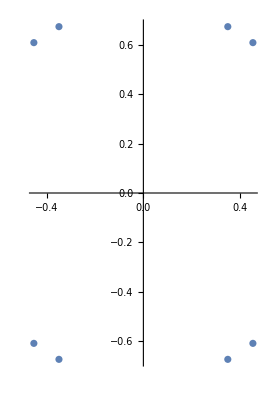

```mathematica
ComplexListPlot[{-0.3492971055250047+0.6747901905492402 ⅈ,0.3492971055250047-0.6747901905492402 ⅈ,-0.3492971055250047-0.6747901905492402 ⅈ,0.3492971055250047+0.6747901905492402 ⅈ,-0.45314655605165916+0.6099249690971389 ⅈ,0.45314655605165916-0.6099249690971389 ⅈ,-0.45314655605165916-0.6099249690971389 ⅈ,0.45314655605165916+0.6099249690971389 ⅈ}]
```